Inter-dye distance distributions (SAWnu)

Theorypaclet:Fretica/tutorial/Inter-DyeDistanceDistributionsSAWnu#77197323 | Applicationpaclet:Fretica/tutorial/Inter-DyeDistanceDistributionsSAWnu#180731379
Definitions (In future part of Fretica?)paclet:Fretica/tutorial/Inter-DyeDistanceDistributionsSAWnu#504587906 |

```mathematica
Needs["Fretica`"]
```

Theory

The “Self-Avoiding-Walk with ν” model (SAWν) is introduced in

-Graphics-

https://doi.org/10.1063/1.5006954https://doi.org/10.1063/1.5006954

This is Eq.5 of this paper

```mathematica
p[r_]=A (4π)/rrms(r/rrms)^(2+g)Exp[-α (r/rrms)^δ]/.{g->(γ-1)/ν,δ->1/(1-ν)}
```

(4 A ⅇ^(-(r/rrms)^(1/(1-ν)) α) π (r/rrms)^(2+(-1+γ)/ν))/rrms

Normalization gives:

```mathematica
p[r_]=p[r]/.A->1/Integrate[p[r]/A,{r,0,∞},Assumptions->{0<ν<1,rrms>0,α>0,γ>1}]
```

-(ⅇ^(-(r/rrms)^(1/(1-ν)) α) (r/rrms)^(2+(-1+γ)/ν) α^(-((-1+ν) (-1+γ+3 ν))/ν))/(rrms (-1+ν) Gamma[-((-1+ν) (-1+γ+3 ν))/ν])

α calculates from:

```mathematica
sol=Solve[rrms^2==Integrate[r^2 p[r],{r,0,∞},Assumptions->{0<ν<1,rrms>0,α>0,γ>1}],α][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{α→(Gamma[-((-1+ν) (-1+γ+3 ν))/ν]/Gamma[-((-1+ν) (-1+γ+5 ν))/ν])^(1/(-2+2 ν))}

```mathematica
p[r_]=p[r]/.sol
```

-((ⅇ^(-(r/rrms)^(1/(1-ν)) (Gamma[-((-1+ν) (-1+γ+3 ν))/ν]/Gamma[-((-1+ν) (-1+γ+5 ν))/ν])^(1/(-2+2 ν))) (r/rrms)^(2+(-1+γ)/ν) ((Gamma[-((-1+ν) (-1+γ+3 ν))/ν]/Gamma[-((-1+ν) (-1+γ+5 ν))/ν])^(1/(-2+2 ν)))^(-((-1+ν) (-1+γ+3 ν))/ν))/(rrms (-1+ν) Gamma[-((-1+ν) (-1+γ+3 ν))/ν]))

```mathematica
Integrate[p[r],{r,0,∞},Assumptions->{0<ν<1,rrms>0,γ>1}]
```

1

```mathematica
Integrate[r^2 p[r],{r,0,∞},Assumptions->{0<ν<1,rrms>0,γ>1}]
```

rrms^2

Definitions (In future part of Fretica?)

### Calculate rrms from ⟨E⟩, p(r) and R_0

```mathematica
FGetRrms[Emean_,p_,R0_]:=Module[{e},
e[rrms_?NumericQ]:=NIntegrate[1/(1+(r/R0)^6)p[rrms][r],{r,0,∞}];
FindRoot[Emean-e[rrms],{rrms,R0}]]
```

### Gaussian chain

```mathematica
FPgc[rrms_][r_]:=(3/(2π))^(3/2)(4π)/rrms(r/rrms)^2 Exp[-3/2 (r/rrms)^2]
```

```mathematica
Integrate[FPgc[rrms][r],{r,0,∞},Assumptions->{rrms>0}]
Integrate[r^2 FPgc[rrms][r],{r,0,∞},Assumptions->{rrms>0}]
```

1

rrms^2

### SAWν

```mathematica
Rationalize[1.1615]
```

2323/2000

```mathematica
FPsawν[rrms_,ν_][r_]:=Block[{a,b,γ},
γ=2323/2000;
a=Gamma[-((-1+ν) (-1+γ+3 ν))/ν];
b=Gamma[-((-1+ν) (-1+γ+5 ν))/ν];
-1/(rrms^3 (-1+ν))ⅇ^(-(r/rrms)^(1/(1-ν)) (a/b)^(1/(-2+2 ν))) r^2 (r/rrms)^((-1+γ)/ν) a^(-(-1+γ+5 ν)/(2 ν)) b^((-1+γ+3 ν)/(2 ν))

]
FPsawν[{b_,n_}][rrms_][r_]:=FPsawν[rrms,Log[rrms/b]/Log[n]][r](* rrms=b n^ν is used; in the absence of additional information, b=0.55nm=Sqrt[2 0.4 nm 0.38 nm] is a good starting point (Hofmann et al. 2012, Zheng et al., 2018, see also Methods of Aznauryan et al., 2016) *)
```

Hofmann et al., Proc Natl Acad Sci U S A. 2012 Oct 2;109(40):16155-60https://doi.org/10.1073/pnas.1207719109

Zheng et al., The Journal of Physical Chemistry B 122(49) 2018https://doi.org/10.1021/acs.jpcb.8b07425

Aznauryan et al., PNAS September 13, 2016 113 (37) E5389-E5398https://doi.org/10.1073/pnas.1607193113

```mathematica
Integrate[FPsawν[rrms,ν][r],{r,0,∞},Assumptions->{0<ν<1,rrms>0}]
```

1

```mathematica
Integrate[r^2 FPsawν[rrms,ν][r],{r,0,∞},Assumptions->{0<ν<1,rrms>0}]
```

rrms^2

```mathematica
FCDFsawν[rrms_,ν_][r_]:=1-Gamma[-((-1+ν) (323+6000 ν))/(2000 ν),r^(1/(1-ν)) rrms^(1/(-1+ν)) (Gamma[-((-1+ν) (323+6000 ν))/(2000 ν)]/Gamma[-((-1+ν) (323+10000 ν))/(2000 ν)])^(1/(-2+2 ν))]/Gamma[-((-1+ν) (323+6000 ν))/(2000 ν)]
```

```mathematica
FCDFsawν[{b_,n_}][rrms_][r_]:=FCDFsawν[rrms,Log[rrms/b]/Log[n]][r]
```

### FTaucOverTaur

Eq. 13 of  Gopich et al. J. Chem. Phys. 131, 095102 (2009)

https://doi.org/10.1063/1.3212597https://doi.org/10.1063/1.3212597

```mathematica
FTauCTimesD[distancePDF_,measuredvariable_,{r1_,r2_}]:=
Block[{p,n,r,norm,nmean,nmeansq,ndiff},
norm=NIntegrate[distancePDF[r],{r,r1,r2}];
p[r_]:=distancePDF[r]/norm;
n[r_]:=measuredvariable[r];
nmean=NIntegrate[n[r]p[r],{r,r1,r2}];
nmeansq=NIntegrate[n[r]^2 p[r],{r,r1,r2}]-nmean^2;
ndiff[r_?NumericQ]:=NIntegrate[(n[ρ]-nmean)p[ρ],{ρ,r1,r}];
NIntegrate[p[r]^-1*ndiff[r]^2,{r,r1,r2}]/nmeansq
]
```

```mathematica
FTaucOverTaur[distancePDF_,measuredvariable_,{r1_,r2_}]:=FTauCTimesD[distancePDF,measuredvariable,{r1,r2}]/FTauCTimesD[distancePDF,#&,{r1,r2}]
```

Application

### Getting r_RMS from mean transfer efficiency E

```mathematica
Map[Plot[{FPgc[#][r],FPsawν[{0.55,50}][#][r]},{r,0,14},ImageSize->200,PlotLabel->"r_RMS="<>ToString[#],PlotLegends->{"GC","SAWν"}]&,{3,5,7}]
```

-Graphics-

```mathematica
nu=Log[rrms/b]/Log[n]/.{rrms->5.,b->0.55,n->50} (* scaling exponent *)
```

0.564229

```mathematica
b=0.55;n=100;
FGetRrms[0.3,FPsawν[{b,n}],5.4]
```

{rrms→7.87821}

```mathematica
FGetRrms[0.3,FPgc,5.4]
```

{rrms→8.31555}

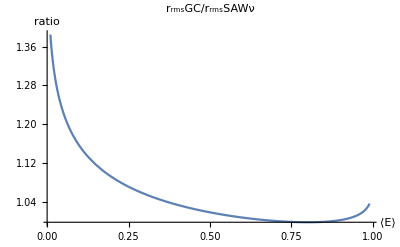

```mathematica
Plot[(rrms/.FGetRrms[EFRET,FPgc,5.4])/(rrms/.FGetRrms[EFRET,FPsawν[{b,n}],5.4]),{EFRET,0.01,0.99},AxesLabel->{"⟨E⟩","ratio"},PlotRange->All,PlotLabel->"r_rmsGC/r_rmsSAWν"] (* ratio illustrates the problem of the Gaussian chain for expanded chains *)
```

### Interpreting nsFCS data: τ_c/τ_r

τ_c is the decay times determined from the donor-donor intensity correlation function.
τ_r is the relaxation time of the end-to-end distance correlation function.
Compare to Eq. 13  and Fig.3  in  Gopich et al. J. Chem. Phys. 131, 095102 (2009)

https://doi.org/10.1063/1.3212597https://doi.org/10.1063/1.3212597

```mathematica
τcoverτrGC=ParallelTable[{rrms,FTaucOverTaur[FPgc[rrms],(1-1/(1+(#)^6))&,{0.01,4*rrms}]},{rrms,0.2,2.75,0.1}];
```

```mathematica
FTaucOverTaurSAWν[{b_,n_}][rrms_]:=Block[{r2},FTaucOverTaur[FPsawν[{b,n}][rrms],(1-1/(1+(#)^6))&,{0.1,r2/.FindRoot[FCDFsawν[{b,n}][rrms][r2]==0.99 ,{{r2,rrms}}]}]]
```

```mathematica
R0:=4.6;
FTaucOverTaurSAWν[{0.55/R0,36}][3.8/R0]
```

0.984

```mathematica
Clear[τcoverτrSawν]
τcoverτrSawν[{b_,n_}]:=τcoverτrSawν[{b,n}]=ParallelTable[{rrms,FTaucOverTaurSAWν[{b,n}][rrms]},{rrms,2*b,Min[2.75,b (n-5)],0.1}]
```

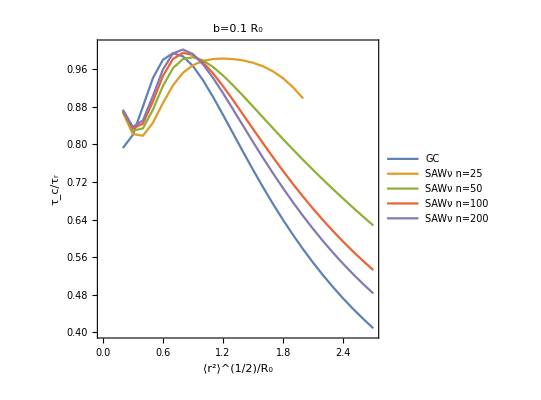

```mathematica
ListPlot[{τcoverτr,τcoverτrSawν[{0.1,25}],τcoverτrSawν[{0.1,50}],τcoverτrSawν[{0.1,100}],τcoverτrSawν[{0.1,200}]},Joined->True,PlotRange->{0.4,1.01},AspectRatio->1,Frame->True,FrameLabel->{"⟨r^2⟩^(1/2)/R_0","τ_c/τ_r"},FrameStyle->18,PlotLegends->{"GC","SAWν n=25","SAWν n=50","SAWν n=100","SAWν n=200"},PlotLabel->"b=0.1 R_0"]
```

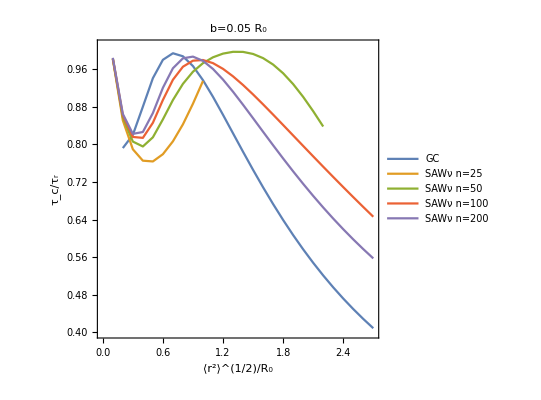

```mathematica
ListPlot[{τcoverτr,τcoverτrSawν[{0.05,25}],τcoverτrSawν[{0.05,50}],τcoverτrSawν[{0.05,100}],τcoverτrSawν[{0.05,200}]},Joined->True,PlotRange->{0.4,1.01},AspectRatio->1,Frame->True,FrameLabel->{"⟨r^2⟩^(1/2)/R_0","τ_c/τ_r"},FrameStyle->18,PlotLegends->{"GC","SAWν n=25","SAWν n=50","SAWν n=100","SAWν n=200"},PlotLabel->"b=0.05 R_0"]
```

```mathematica
0.38/5.4
```

0.0703704

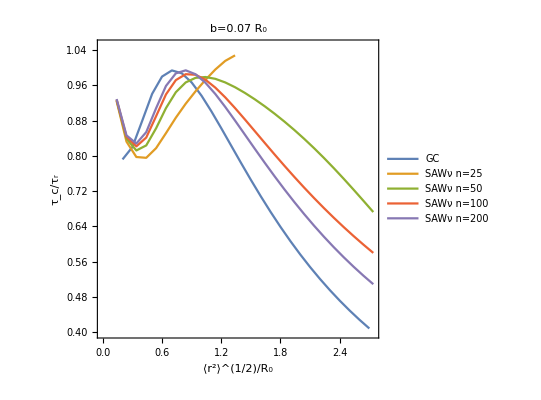

```mathematica
ListPlot[{τcoverτr,τcoverτrSawν[{0.07,25}],τcoverτrSawν[{0.07,50}],τcoverτrSawν[{0.07,100}],τcoverτrSawν[{0.07,200}]},Joined->True,PlotRange->{0.4,1.05},AspectRatio->1,Frame->True,FrameLabel->{"⟨r^2⟩^(1/2)/R_0","τ_c/τ_r"},FrameStyle->18,PlotLegends->{"GC","SAWν n=25","SAWν n=50","SAWν n=100","SAWν n=200"},PlotLabel->"b=0.07 R_0"]
```

| Related Guides
▪Fretica